# LIPSS: Sipe-Theory-calculation

[1] = J. E. Sipe, Jeff F. Young, J. S. Preston, and H. M. van Driel
Laser-induced periodic surface structure. I. Theory
Phys. Rev. B 27, 1141

[2] = J. Bonse, M. Munz, H. Sturm; 
Structure formation on the surface of indium phosphide irradiated by femtosecond laser pulses. 
J. Appl. Phys. 1 January 2005; 97 (1)

```mathematica
Ref=Column[{TextCell["References:","Text",Directive[FontFamily->"Times",FontSize->16]],TextCell["- J.E.Sipe, Jeff F.Young, J.S.Preston, and H.M.van Driel; Laser-induced periodic surface structure. I. Theory Phys. Rev. B 27, 1141","Text",Directive[FontFamily->"Times",FontSize->16]],TextCell["- J.Bonse, M.Munz, H.Sturm; Structure formation on the surface of indium phosphide irradiated by femtosecond laser pulses. J. Appl. Phys. 1 January 2005; 97 (1)","Text",Directive[FontFamily->"Times",FontSize->16]],TextCell["- D.Kaczmarek, T.J.Albert, J.Bonse; Erratum: Structure formation on the surface of indium phosphide irradiated by femtosecond laser pulses","Text",Directive[FontFamily->"Times",FontSize->16]]}];
```

## Input of material properties

in general: first evaluate cell then enter or select parameters

```mathematica
Print[Grid[{{Panel[Row[{"Material:", InputField[Dynamic[M],FieldHint->"Ti, Si, etc."]}]],Panel[Row[{"Wavelengh [nm]:", InputField[Dynamic[Λ]]}]],Panel[Row[{"Angle of incidence [°]:", InputField[Dynamic[θ],FieldHint->"[°]"]}]]},{Panel[Row[{"Refractive index n:", InputField[Dynamic[nc]]}]],Panel[Row[{"Optical extinction coefficient k:", InputField[Dynamic[kc]]}]],Panel[Row[{"Shape-factor s:", InputField[Dynamic[s]]}]],Panel[Row[{"Filling-factor F:", InputField[Dynamic[F]]}]]}},Alignment->Left]]
```

Material: | Wavelengh [nm]: | Angle of incidence [°]: | 
Refractive index n: | Optical extinction coefficient k: | Shape-factor s: | Filling-factor F:

```mathematica
GraphicLabel=TextCell[Row[{"Sipe-Calculation of ",Dynamic[M]," @ λ = ",Dynamic[Λ]," nm, θ = ",Dynamic[θ],"°, n = ",Dynamic[nc],"+i",Dynamic[kc],", s = ",Dynamic[s],", F = ",Dynamic[F]}],{"Text"},Directive[FontFamily->"Times",FontSize->16]]
```

Sipe-Calculation of  @ λ =  nm, θ = °, n = +i, s = , F =

## choose orientation of scattering pattern

changes the orientation by 90°

```mathematica
Grid[{{"choose orientation:",RadioButtonBar[Dynamic[o],{0->"horizontal",1->"vertical"}]}}]
```

choose orientation: |  | horizontal   | vertical

## Angle of incidence

calculates the angle of incidence in [rad]

```mathematica
Θ[θ_]:=θ*Pi/180 
Θ[θ]
```

π/3

## optical properties

```mathematica
Dynamic[ϵrc=Re[(nc+I*kc)^2]]
Dynamic[ϵimc=Im[(nc+I*kc)^2]]
Dynamic[ϵ=ϵrc+I*ϵimc]
R[ϵ_]:=(ϵ-1)/(ϵ+1) (*in the text after Eq.12 Ref.[2]*)
```

## help-functions

```mathematica
h[s_]:=Sqrt[s^2+1]-s (*Eq.13 Ref.[2]*)
hI[s_]:=0.5*(Sqrt[(s^2)+4]+s)-Sqrt[(s^2)+1](*Eq.14 Ref.[2]*)
γt[ϵ_,F_,s_]:=(ϵ-1)/(4*Pi*(1+0.5*(1-F)*(ϵ-1)*(h[s]-R[ϵ]*hI[s])))(*in the text after Eq.12 Ref.[2]*)
γz[ϵ_,F_,s_]:=(ϵ-1)/(4*Pi*(ϵ-(1-F)*(ϵ-1)*(h[s]+R[ϵ]*hI[s])))(*in the text after Eq.12 Ref.[2]*)
hss[ϵ_,κ_]:=(2*I)/(Sqrt[1-κ^2]+Sqrt[ϵ-κ^2])(*Eq.5 Ref.[2]*)
hkk[ϵ_,κ_]:=(2*I*Sqrt[ϵ-κ^2]*Sqrt[1-κ^2])/(ϵ*Sqrt[1-κ^2]+Sqrt[ϵ-κ^2])(*Eq.6 Ref.[2]*)
hzz[ϵ_,κ_]:=(2*I*κ^2)/(ϵ*Sqrt[1-κ^2]+Sqrt[ϵ-κ^2])(*Eq.9 Ref.[2]*)
hzk[ϵ_,κ_]:=(2*I*κ*Sqrt[1-κ^2])/(ϵ*Sqrt[1-κ^2]+Sqrt[ϵ-κ^2])(*Eq.8 Ref.[2]*)
hkz[ϵ_,κ_]:=(2*I*κ*Sqrt[ϵ-κ^2])/(ϵ*Sqrt[1-κ^2]+Sqrt[(ϵ-κ^2)])(*Eq.7 Ref.[2]*)
```

## Fresnel-Coefficients

```mathematica
tsκi[ϵ_,κ_]:=(2)/(1+Sqrt[(ϵ-κ^2)/(1-κ^2)])(*Eq.10 Ref.[2]*)
tpκi[ϵ_,κ_]:=(2*Sqrt[ϵ])/(ϵ+Sqrt[(ϵ-κ^2)/(1-κ^2)])
txκi[ϵ_,κ_]:=tpκi[ϵ,κ]*Sqrt[1-(κ^2/ϵ)](*Eq.11 Ref.[2]*)
tzκi[ϵ_,κ_]:=tpκi[ϵ,κ]*(κ/Sqrt[ϵ])(*Eq.12 Ref.[2]*)
```

## κ+ and κ-

```mathematica
If[o==0,κplus[κx_,κy_,θ_]:=Sqrt[(Sin[Θ[θ]]+κx)^2+κy^2],κplus[κx_,κy_,θ_]:=Sqrt[(Sin[Θ[θ]]+κy)^2+κx^2]](*in the text after Eq.4 Ref.[2]*)
If[o==0,κminus[κx_,κy_,θ_]:=Sqrt[(Sin[Θ[θ]]-κx)^2+κy^2],κminus[κx_,κy_,θ_]:=Sqrt[(Sin[Θ[θ]]-κy)^2+κx^2]](*in the text after Eq.4 Ref.[2]*)
```

```mathematica
hssplus[ϵ_,κx_,κy_,θ_]:=hss[ϵ,κplus[κx,κy,θ]]
hssminus[ϵ_,κx_,κy_,θ_]:=hss[ϵ,κminus[κx,κy,θ]]
hkkplus[ϵ_,κx_,κy_,θ_]:=hkk[ϵ,κplus[κx,κy,θ]]
hkkminus[ϵ_,κx_,κy_,θ_]:=hkk[ϵ,κminus[κx,κy,θ]]
hzzplus[ϵ_,κx_,κy_,θ_]:=hzz[ϵ,κplus[κx,κy,θ]]
hzzminus[ϵ_,κx_,κy_,θ_]:=hzz[ϵ,κminus[κx,κy,θ]]
hzkplus[ϵ_,κx_,κy_,θ_]:=hzk[ϵ,κplus[κx,κy,θ]]
hzkminus[ϵ_,κx_,κy_,θ_]:=hzk[ϵ,κminus[κx,κy,θ]]
hkzplus[ϵ_,κx_,κy_,θ_]:=hkz[ϵ,κplus[κx,κy,θ]]
hkzminus[ϵ_,κx_,κy_,θ_]:=hkz[ϵ,κminus[κx,κy,θ]]
```

## κ -> sin(θ)

```mathematica
ts[ϵ_,θ_]:=tsκi[ϵ,Sin[Θ[θ]]]
tx[ϵ_,θ_]:=txκi[ϵ,Sin[Θ[θ]]]
tz[ϵ_,θ_]:=tzκi[ϵ,Sin[Θ[θ]]]
```

## inner products

```mathematica
If[o==0,kpx[κx_,κy_,θ_]:=(Sin[Θ[θ]]+κx)/(κplus[κx,κy,θ]),kpx[κx_,κy_,θ_]:=(κx)/(κplus[κx,κy,θ])](*Eq.4 Ref.[2]*)
If[o==0,kmx[κx_,κy_,θ_]:=(Sin[Θ[θ]]-κx)/(κminus[κx,κy,θ]),kmx[κx_,κy_,θ_]:=(-κx)/(κminus[κx,κy,θ])](*Eq.4 Ref.[2]*)
If[o==0,kpy[κx_,κy_,θ_]:=(κy)/(κplus[κx,κy,θ]),kpy[κx_,κy_,θ_]:=(Sin[Θ[θ]]+κy)/(κplus[κx,κy,θ])](*Eq.3 Ref.[2]*)
If[o==0,kmy[κx_,κy_,θ_]:=(-κy)/(κminus[κx,κy,θ]),kmy[κx_,κy_,θ_]:=(Sin[Θ[θ]]-κy)/(κminus[κx,κy,θ])](*Eq.3 Ref.[2]*)
```

## complex function ν for s-pol. and p-pol

```mathematica
If[o==0,νplusspol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]^2+hkkplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[ts[ϵ,θ]]^2,νplusspol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]^2+hkkplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[ts[ϵ,θ]]^2](*Eq.2a Ref.[2]*)
If[o==0,νminusspol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]^2+hkkminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[ts[ϵ,θ]]^2,νminusspol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]^2+hkkminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[ts[ϵ,θ]]^2](*Eq.2a Ref.[2]*)
If[o==0,νplusppol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]^2+hkkplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[tx[ϵ,θ]]^2+hkzplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]*γz[ϵ,F,s]*ϵ*Conjugate[tx[ϵ,θ]]*tz[ϵ,θ]+hzkplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]*γt[ϵ,F,s]*Conjugate[tz[ϵ,θ]]*tx[ϵ,θ]+hzzplus[ϵ,κx,κy,θ]*γz[ϵ,F,s]*ϵ*Abs[tz[ϵ,θ]]^2,νplusppol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssplus[ϵ,κx,κy,θ]*kpx[κx,κy,θ]^2+hkkplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[tx[ϵ,θ]]^2+hkzplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]*γz[ϵ,F,s]*ϵ*Conjugate[tx[ϵ,θ]]*tz[ϵ,θ]+hzkplus[ϵ,κx,κy,θ]*kpy[κx,κy,θ]*γt[ϵ,F,s]*Conjugate[tz[ϵ,θ]]*tx[ϵ,θ]+hzzplus[ϵ,κx,κy,θ]*γz[ϵ,F,s]*ϵ*Abs[tz[ϵ,θ]]^2](*Eq.2b Ref.[2]*)
If[o==0,νminusppol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]^2+hkkminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[tx[ϵ,θ]]^2+hkzminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]*γz[ϵ,F,s]*ϵ*Conjugate[tx[ϵ,θ]]*tz[ϵ,θ]+hzkminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]*γt[ϵ,F,s]*Conjugate[tz[ϵ,θ]]*tx[ϵ,θ]+hzzminus[ϵ,κx,κy,θ]*γz[ϵ,F,s]*ϵ*Abs[tz[ϵ,θ]]^2,νminusppol[ϵ_,κx_,κy_,θ_,F_,s_]:=(hssminus[ϵ,κx,κy,θ]*kmx[κx,κy,θ]^2+hkkminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]^2)*γt[ϵ,F,s]*Abs[tx[ϵ,θ]]^2+hkzminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]*γz[ϵ,F,s]*ϵ*Conjugate[tx[ϵ,θ]]*tz[ϵ,θ]+hzkminus[ϵ,κx,κy,θ]*kmy[κx,κy,θ]*γt[ϵ,F,s]*Conjugate[tz[ϵ,θ]]*tx[ϵ,θ]+hzzminus[ϵ,κx,κy,θ]*γz[ϵ,F,s]*ϵ*Abs[tz[ϵ,θ]]^2](*Eq.2b Ref.[2]*)
```

## efficacy factor η for s-pol. and p-pol

```mathematica
ηspol[ϵ_,κx_,κy_,θ_,F_,s_]:=2*Pi*Abs[νplusspol[ϵ,κx,κy,θ,F,s]+Conjugate[νminusspol[ϵ,κx,κy,θ,F,s]]](*Eq.1 Ref.[2]*)
ηppol[ϵ_,κx_,κy_,θ_,F_,s_]:=2*Pi*Abs[νplusppol[ϵ,κx,κy,θ,F,s]+Conjugate[νminusppol[ϵ,κx,κy,θ,F,s]]](*Eq.1 Ref.[2]*)
```

## get Data

the generation of Data (array 801x801 pixel) takes approx. 4 Minutes

```mathematica
DataS=Reverse[Transpose[Table[ηspol[ϵ,κx,κy,θ,F,s],{κx,-4,4,0.01},{κy,-4,4,0.01}]]];//AbsoluteTiming
```

{49.6182,Null}

```mathematica
DataP=Reverse[Transpose[Table[ηppol[ϵ,κx,κy,θ,F,s],{κx,-4,4,0.01},{κy,-4,4,0.01}]]];//AbsoluteTiming
```

{170.402,Null}

## visualization of the Data

```mathematica
{MinDataSPol=Min[DataS],MinDataPPol=Min[DataP],MaxDataSPol=Max[DataS],MaxDataPPol=Max[DataP]};(*for rescaling the colorbar*)
{PlotSPol=Dynamic[ArrayPlot[DataS,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{MinDataSPol,MaxDataSPol},{0,1}]]&),ColorFunctionScaling->False,Frame->True,FrameStyle->Directive[Thick,Black],Axes->True,AxesOrigin->{400,400},AxesStyle->Thickness[0.005],FrameLabel->{TraditionalForm["Normalized"Subscript[κ,y]],TraditionalForm["Normalized"Subscript[κ,x]],None,"s-pol. 2D Map of efficacy factor η"},LabelStyle->Directive[FontFamily->"Times",FontColor->Black,FontSize->16],FrameTicks->{{{{800,-4},{600,-2},{400,0},{200,2},{0,4}},None},{{{0,-4},{200,-2},{400,0},{600,2},{800,4}},None}},PlotLegends->Automatic,ImageSize->450]],PlotPPol=Dynamic[ArrayPlot[DataP,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{MinDataPPol,MaxDataPPol},{0,1}]]&),ColorFunctionScaling->False,Frame->True,FrameStyle->Directive[Thick,Black],Axes->True,AxesOrigin->{400,400},AxesStyle->Thickness[0.005],FrameLabel->{TraditionalForm["Normalized"Subscript[κ,y]],TraditionalForm["Normalized"Subscript[κ,x]],None,"p-pol. 2D Map of efficacy factor η"},LabelStyle->Directive[FontFamily->"Times",FontColor->Black,FontSize->16],FrameTicks->{{{{800,-4},{600,-2},{400,0},{200,2},{0,4}},None},{{{0,-4},{200,-2},{400,0},{600,2},{800,4}},None}},PlotLegends->Automatic,ImageSize->450]]};
```

## Cross section plot

0° and 90° are already implemented in the code

0° = vertical (along y-axsis)
90° = horizontal (along x-axsis)

choose here an angle between 0 and 90 degrees for a third crosssection plot and the maximal value for the y-axis (for s- and p-pol.):

```mathematica
Print[Row[{Panel[Row[{"Angle of cross section [°]:", InputField[Dynamic[ϕ]]}]],Panel[Row[{"Max. y-axis value for s-pol.:", InputField[Dynamic[y1]]}]],Panel[Row[{"Max. y-axis value for p-pol.:", InputField[Dynamic[y2]]}]]}]]
```

Angle of cross section [°]:Max. y-axis value for s-pol.:Max. y-axis value for p-pol.:

```mathematica
Φ[ϕ_]:=ϕ*Pi/180 ;
lengthscaling=Sqrt[1+Tan[(Pi/2)-Φ[ϕ]]];(*considers the angle between x-axis and intersection*)
CPlotSPol=Show[Plot[ηspol[ϵ,κx,0,θ,F,s],{κx,0,5},PlotStyle->{Thickness[0.0050],Red,Dashed},PlotRange->{Automatic,{0,y1}}],Plot[ηspol[ϵ,0,κy,θ,F,s],{κy,0,5},PlotStyle->{Thickness[0.0050],Blue},PlotRange->{Automatic,{0,y1}}],Plot[ηspol[ϵ,κx/lengthscaling,(κx/lengthscaling)*Tan[(Pi/2)-Φ[ϕ]],θ,F,s],{κx,0,5},PlotStyle->{Thickness[0.0050],Magenta,DotDashed},PlotRange->{Automatic,{0,y1}}],Frame->True,FrameTicks->All,FrameStyle->Directive[Thick,Black],FrameLabel->{{TraditionalForm["Efficacy Factor"η],None},{TraditionalForm["Normalized κ"],"s-pol. cross section plot"}},LabelStyle->Directive[FontFamily->"Times",FontColor->Black,FontSize->16],ImageSize->500];
CrossPlotSPol=Legended[CPlotSPol,LineLegend[{Blue,{Magenta,DotDashed},{Red,Dashed}},{TextCell[Row[{"ϕ = 0°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]],TextCell[Row[{"ϕ = ",Dynamic[ϕ],"°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]],TextCell[Row[{"ϕ = 90°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]]}]];
CPlotPPol=Show[Plot[ηppol[ϵ,κx,0,θ,F,s],{κx,0,5},PlotStyle->{Thickness[0.0050],Red,Dashed},PlotRange->{Automatic,{0,y2}}],Plot[ηppol[ϵ,0,κy,θ,F,s],{κy,0,5},PlotStyle->{Thickness[0.0050],Blue},PlotRange->{Automatic,{0,y2}}],Plot[ηppol[ϵ,κx/lengthscaling,(κx/lengthscaling)*Tan[(Pi/2)-Φ[ϕ]],θ,F,s],{κx,0,5},PlotStyle->{Thickness[0.0050],Magenta,DotDashed},PlotRange->{Automatic,{0,y2}}],Frame->True,FrameTicks->All,FrameStyle->Directive[Thick,Black],FrameLabel->{{TraditionalForm["Efficacy Factor"η],None},{TraditionalForm["Normalized κ"],"p-pol. cross section plot"}},LabelStyle->Directive[FontFamily->"Times",FontColor->Black,FontSize->16],ImageSize->500];
CrossPlotPPol=Legended[CPlotPPol,LineLegend[{Blue,{Magenta,DotDashed},{Red,Dashed}},{TextCell[Row[{"ϕ = 0°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]],TextCell[Row[{"ϕ = ",Dynamic[ϕ],"°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]],TextCell[Row[{"ϕ = 90°"}],{"Text"},Directive[FontFamily->"Times",FontColor->Black,FontSize->16]]}]];
```

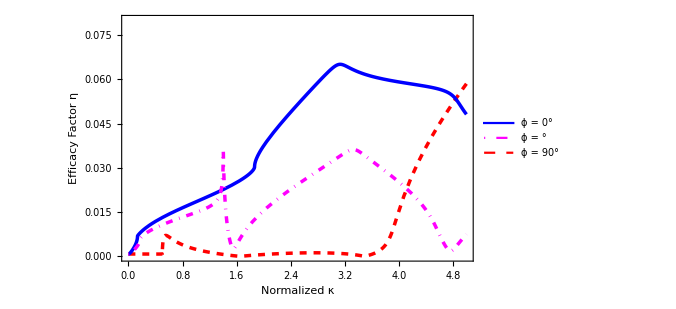
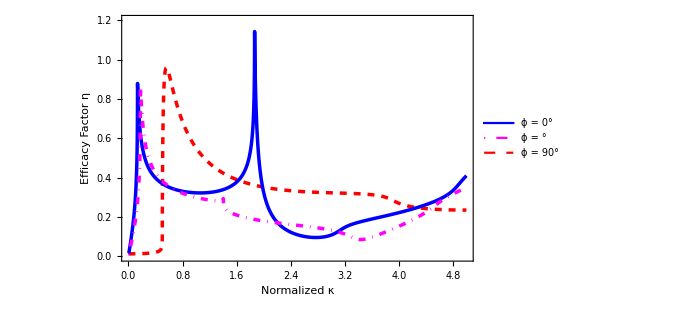
| 
-Graphics- | -Graphics-
References:
- J.E.Sipe, Jeff F.Young, J.S.Preston, and H.M.van Driel; Laser-induced periodic surface structure. I. Theory Phys. Rev. B 27, 1141
- J.Bonse, M.Munz, H.Sturm; Structure formation on the surface of indium phosphide irradiated by femtosecond laser pulses. J. Appl. Phys. 1 January 2005; 97 (1)
- D.Kaczmarek, T.J.Albert, J.Bonse; Erratum: Structure formation on the surface of indium phosphide irradiated by femtosecond laser pulses | Sipe-Calculation of  @ λ =  nm, θ = °, n = +i, s = , F =

```mathematica
FGraphic=Grid[{{PlotSPol,PlotPPol},{CrossPlotSPol,CrossPlotPPol},{Ref,SpanFromLeft}},Spacings->{5,2},Frame->All];
FinalGraphic=Labeled[FGraphic,GraphicLabel,Top]
```

```mathematica
If[o==0,Export["Sipe-Simulation-horizontal"<>#,FinalGraphic]&/@{".pdf",".png",".jpg"},Export["Sipe-Simulation-vertical"<>#,FinalGraphic]&/@{".pdf",".png",".jpg"}];
```